```mathematica
Clear@Evaluate[Context[]<>"*"]
```

```mathematica
{(-(l+1-x)x)/(l+x)(-1)^l∏_(k=1)^l (k^2-x^2),Gamma[l+x]/Gamma[-l-1+x]}//FullSimplify[Equal@@#,{l∈Integers}]&
```

True

```mathematica
{(-(l+1+x)x)/(l-x)(-1)^l∏_(k=1)^l (k^2-x^2),Gamma[l+2+x]/Gamma[-l+1+x]}//FullSimplify[Equal@@#,{l∈Integers}]&
```

True

```mathematica
Gamma[l+2+x]/Gamma[-l+1+x]==∏_(k=-l+1)^(l+1) (k+x)(*s=-1*)
%//FullSimplify
```

Gamma[2+l+x]/Gamma[1-l+x]==Pochhammer[1-l+x,1+2 l]

True

```mathematica
Gamma[l+x]/Gamma[-l-1+x]==∏_(k=-l-1)^(l-1) (k+x)(*s=+1*)
%//FullSimplify
```

Gamma[l+x]/Gamma[-1-l+x]==Pochhammer[-1-l+x,1+2 l]

True

```mathematica
expansionP=(ParallelTable[Limit[Pochhammer[-1-l+x,1+2 l]//Normal@Series[#,{x,0,1}]&,l->ℓ],{ℓ,1,15}]/x)//FindSequenceFunction[{Range[1,15],#}ᵀ,ℓ]&//FullSimplify
```

(-1)^(1+ℓ) Gamma[ℓ] Gamma[2+ℓ]

```mathematica
expansionM=(ParallelTable[Limit[Pochhammer[1-l+x,1+2 l]//Normal@Series[#,{x,0,1}]&,l->ℓ],{ℓ,1,15}]/x)//FindSequenceFunction[{Range[1,15],#}ᵀ,ℓ]&//FullSimplify
```

(-1)^(1+ℓ) Gamma[ℓ] Gamma[2+ℓ]

```mathematica
∏_(k=-l-s)^(l-s) (k+x)//FunctionExpand
```

Gamma[1+l-s+x]/Gamma[-l-s+x]

```mathematica
ParallelTable[Limit[Gamma[-2l-1]/Gamma[2l+1] Gamma[l+1]/Gamma[-l]/.{l->ℓ+ϵ},ϵ->0],{ℓ,0,20}]//FindSequenceFunction[{Range[0,20],#}ᵀ,l]&//FullSimplify[#,{l∈Integers,l≥0}]&
```

((-1)^(1+l) 2^(-1-4 l))/(Pochhammer[1/2,l] Pochhammer[3/2,l])

```mathematica
ParallelTable[Limit[Gamma[-2l]/Gamma[-l+1] Gamma[l+2]/Gamma[2l+2]/.{l->ℓ+ϵ},ϵ->0],{ℓ,1,20}]//FindSequenceFunction[{Range[1,20],#}ᵀ,l]&//FullSimplify[#,{l∈Integers,l≥0}]/.{Gamma[α_+l]->Gamma[α]Pochhammer[α,l]}&
```

((-1)^(1+l) 2^(-1-4 l) (1+l))/(l Pochhammer[1/2,l] Pochhammer[3/2,l])

```mathematica
Exp@Sum[Normal@Series[Log[4(τ ω k)^2+(4ω χ)^2],{χ,0,2}],{k,1,ℓ}]//Simplify
```

4^ℓ ⅇ^((4 χ^2 HarmonicNumber[ℓ,2])/τ^2) (τ^2 ω^2)^ℓ Gamma[1+ℓ]^2

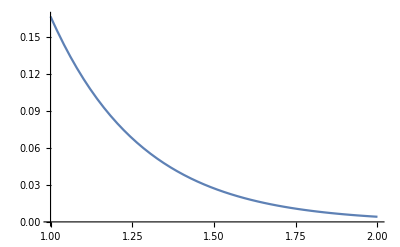

```mathematica
(Gamma[ℓ]Gamma[ℓ+1]Gamma[ℓ+2])/(Gamma[2ℓ+2]Gamma[2ℓ+1])//Plot[#,{ℓ,1,2}]&
```

```mathematica
ⅇ^(-x^2 HarmonicNumber[1,2])
```

ⅇ^(-x^2)

```mathematica
D[ⅇ^(-x^2), x]
```

-2 ⅇ^(-x^2) x

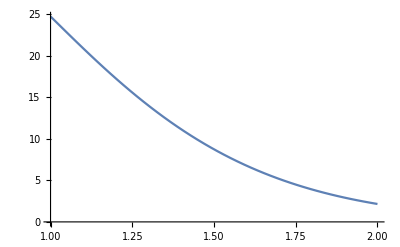

```mathematica
(Gamma[ℓ]Gamma[ℓ+1]Gamma[ℓ+2])/(Gamma[2ℓ+2]Gamma[2ℓ+1])ⅇ^(10HarmonicNumber[ℓ,2]/2) //Plot[#,{ℓ,1,2}]&
```